```mathematica
ClearAll["Global`*"]
```

## Common

```mathematica
RestylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/.{__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]];
```

```mathematica
dashingStyle = Dashing[{maxt/2,maxt/2-maxt/10}];
```

```mathematica
pathToOutput=ToString["\..\plots\delay\\"];
```

## Step response

### TF function

```mathematica
k=10;
maxt = 4;
τ=1;
TFsimple=k * SystemsModelDelay[1];
TF=TransferFunctionModel[TFsimple,s];
TFstep=Simplify[OutputResponse[TF,UnitStep[t],t]];
TFstepf[t_]=TFstep;
TFstableValue=Limit[TFstep,t->Infinity][[1]];
```

Thread::tdlen: Objects of unequal length in {}+{10 1 UnitStep[t]} cannot be combined.

Thread::tdlen: Objects of unequal length in {}+{10 UnitStep[-1+t]} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

```mathematica
TF
```

10 1TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s111011FalseFalseFalseAutomaticNoneAutomatic

### Sizes

#### Common

```mathematica
arrowsHeads=Arrowheads[{-.035,.035}];
sizeText[text_]:=Style[text, 18,FontSlant->Italic,FontFamily->"Times New Roman"];
```

#### Vertical size

```mathematica
verSizeText=Text[
sizeText["k"],
{
-0.05,
TFstableValue
}
];
```

### Plot

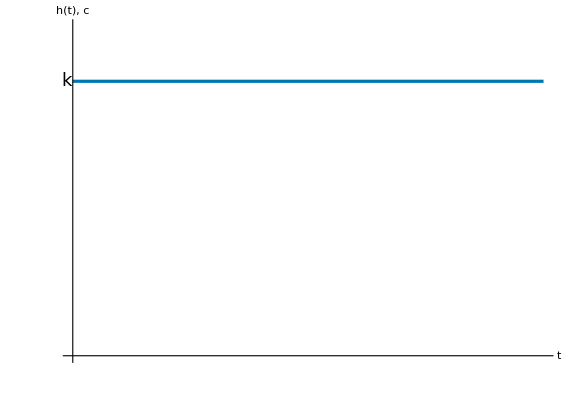

```mathematica
tickXStep = 1/2;
tickYStep = 1;
stepRespPic=Plot[{TFstep},{t, 0, maxt },
AxesStyle->Directive[Black, FontSize->9],
AxesLabel->{sizeText["t"], sizeText["h(t), c"]},
GridLines->None,
PlotStyle->{{RGBColor["#0077b5"],Thickness[0.004]},{Black,dashingStyle}},
PlotRange->{{0,maxt },{0,TFstableValue*1.2}},
PlotRangeClipping->False,
ImageSize->Large,
Ticks->{(#&@Array[{tickXStep #,}&,100]),(#&@Array[{tickYStep #,}&,100])},
AspectRatio->11/16,
Epilog->{
{verSizeText}
}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"step.svg";
Export[fName,stepRespPic];
```

### Log Plot

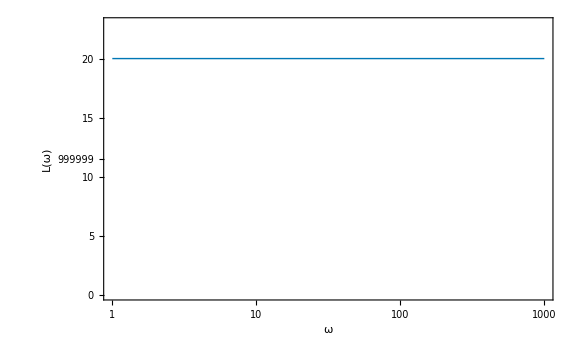

```mathematica
bodePlot=BodePlot[TF,{1,10^3},PlotRange->{{0,23},Automatic},
PlotStyle->Thickness[0.004],
ImageSize->Large
];
ampBodePlot=RestylePlot[
bodePlot[[1,1,1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-apm-freq.svg";
Export[fName,ampBodePlot];
```

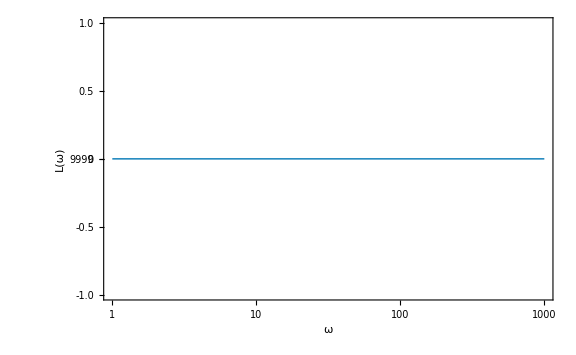

```mathematica
phaseBodePlot=RestylePlot[
bodePlot[[1,2,1]],
{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["L(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"log-phase-freq.svg";
Export[fName,phaseBodePlot];
```

### Plot

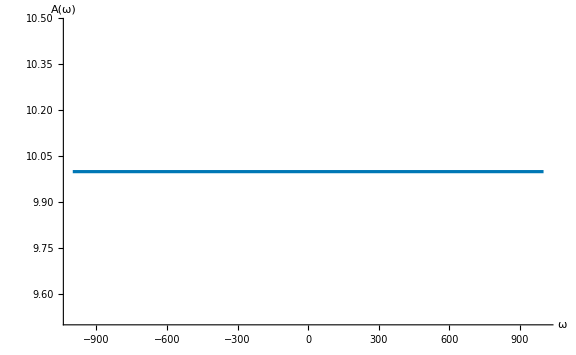

```mathematica
ampPlot=Plot[Abs[TF[I f]], {f, -1000, 1000},
(*PlotRange->{{0,Full},{0,10}},*)
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ω"],sizeText["A(ω)"]},
LabelStyle->{
FontFamily->"Arial",14,Black
},
(*Ticks->{
Prepend[(#&@Array[{100#,}&,100]),{0,0}],
(#&@Array[{2#,}&,100])
},*)
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"amp-freq.svg";
Export[fName,ampPlot];
```

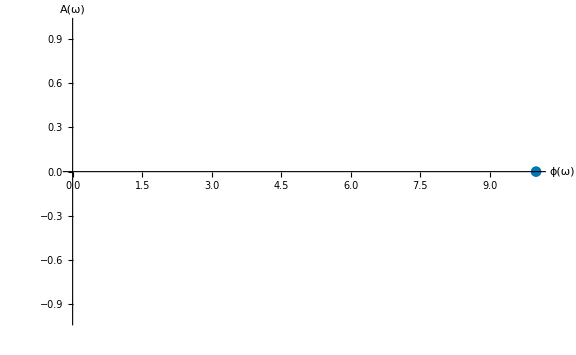

```mathematica
nyquistPlot=NyquistPlot[TF,
(*PlotRange->{{0,Full},{0,10}},*)
PlotStyle->{RGBColor["#0077b5"],Thickness[0.004]},
AxesLabel->{sizeText["ϕ(ω)"],sizeText["A(ω)"]},
AxesOrigin->{0,0},
LabelStyle->{
FontFamily->"Arial",14,Black
},
PlotRangeClipping->False,
ImageSize->Large,
ImagePadding->{{All, All},{50, 30}}
]
```

```mathematica
fName=ParentDirectory[NotebookDirectory[]]<>pathToOutput<>"nyquist.svg";
Export[fName,nyquistPlot];
```